# Mi primer notebook

## por: J. Orduz

Esta es mi primer gráfica

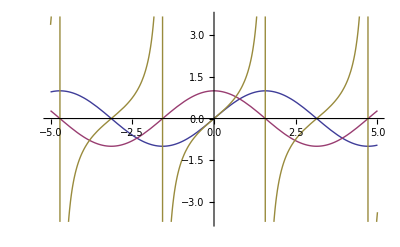

```mathematica
Plot[{Sin[x], Cos[x],Tan[x]},{x,-5,5}]
```

```mathematica
fn[x_,y_,z_]:=x+y* z^3;
```

```mathematica
fn[1,2,z]
```

2 z^3+1

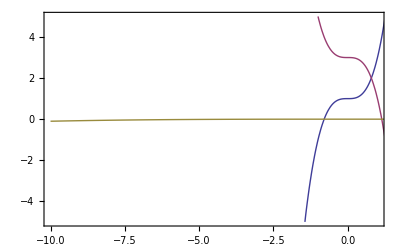

```mathematica
Plot[{fn[1,2,z],fn[3,-2,z],fn[0.00003,0.0001,z]},{z,-10,10},PlotRange->{{-10,1},{-5,5}},Frame->True]
```

```mathematica
Length[(x^2+3x+2)*(x)]
```

2

```mathematica
fns[x_]:={2*x+5,x+6};
```

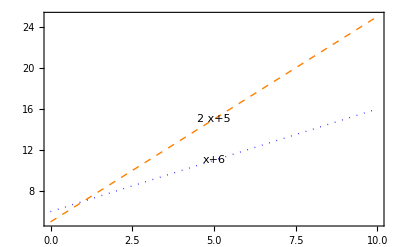

```mathematica
len:=Length[fns[x]];

Plot[Evaluate[fns[x]],{x,0,10},Epilog->Table[Inset[DisplayForm[fns[x][[i]]],{5,fns[5][[i]]},Background->White],{i,len}],PlotStyle->{{Orange,Dashed},{Blue,Dotted},{Magenta,DotDashed}}, Frame->True]
```

esta es otra cosa

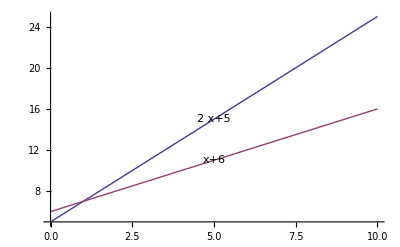

```mathematica
Plot[Evaluate[fns[x]],{x,0,10},Epilog->Table[Inset[Framed[DisplayForm[fns[x][[i]]],RoundingRadius->5],{5,fns[5][[i]]},Background->White],{i,len}]]
```

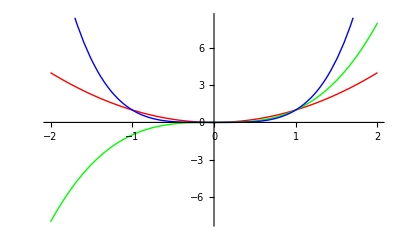

```mathematica
Plot[Tooltip@{x^2,x^3,x^4},{x,-2,2},PlotStyle->{Red,Green,Blue},PlotRangePadding->1.3]/.{Tooltip[{_,color_,line_},tip_]:>{Text[Style[tip(*"f"*),14],{.1,0.7}+line[[1,-1]]],color,line}}
```

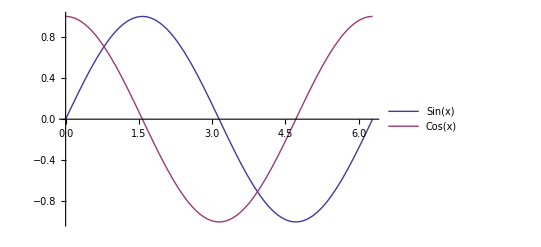

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotLegends->{"Sin(x)","Cos(x)"}]
```

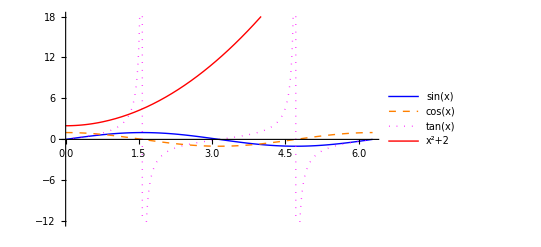

```mathematica
Plot[{Sin[x],Cos[x], Tan[x],x^2+2},{x,0,2π},PlotLegends->"Expressions",PlotStyle->{{Blue},{Orange,Dashed},{Magenta,Dotted},{Red}}]
```

```mathematica
f[aa_,x_,y_]:=y*Sin[3 x y]+x^2-aa
g[aa_,x_,y_]:=(x*Sin[x y])^2-aa
h[aa_,x_,y_]:=(Sin[x^3 y])^2-2*aa
MyRegion[a_,b_,aa_,colorp_]:=RegionPlot[a[f[aa,x,y],0]&&b[g[aa,x,y],h[aa,x,y]],{x,-5,5},{y,-5,5},Axes->True,BoundaryStyle->None,PlotStyle->{Directive[colorp,Opacity[0.4]]}];
shadingfig341LG:=GraphicsGrid[Table[MyRegion[a,b,1,Red],{a,{Less}},{b,{Greater}}]]
shadingfig342LG:=GraphicsGrid[Table[MyRegion[a,b,3,Blue],{a,{Less}},{b,{Greater}}]]
Rasterize[Show[{shadingfig341LG,shadingfig342LG}],RasterSize->700,ImageResolution->900]
(*shadingfig34GL:=GraphicsGrid[Table[MyRegion[a,b,Blue],{a,{Less}},{b,{Less}}]]
Show[{shadingfig34LG, shadingfig34GL}]*)
```

-Graphics-

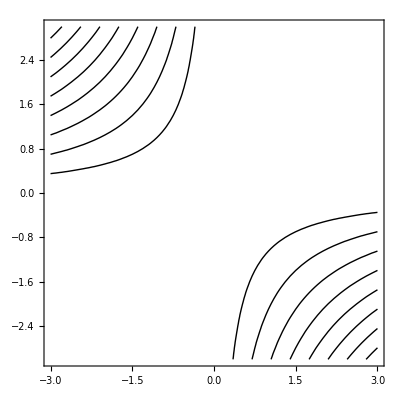

```mathematica
t1=Table[If[x*y<0,Sin[3 x*y],Sequence[]],{x,-3,3,.1},{y,-3,3,.1}];

ListContourPlot[t1,Contours->{0},ContourShading->False,DataRange->{{-3,3},{-3,3}},RegionFunction->Function[{x,y},x*y<0],ContourStyle->Black]
```

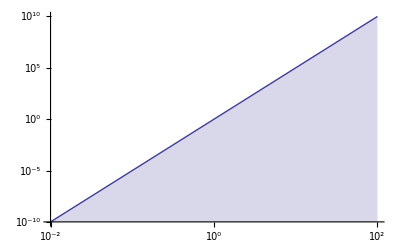

```mathematica
xticks=Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-2,2,2}];
yticks=Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-10,10,5}];
LogLogPlot[x^5,{x,10^-2,10^2},Ticks->{xticks,yticks},Filling->Bottom]
```

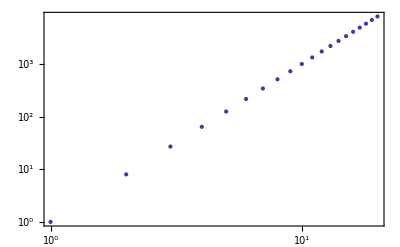

```mathematica
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript[10,i],Spacer[{0,0}]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0.},{Thickness[0.001]}},{i,min10,max10},{k,9}],1]]]

ListLogLogPlot[Range[20]^3,Frame->True,FrameTicks->{{PowerTicks[True],PowerTicks[False]},{PowerTicks[True],PowerTicks[False]}}]
```

## Referencees [1]http://stackoverflow.com/questions/7860400/exponential-form-of-tick-marks-for-log-plot-in-mathematica